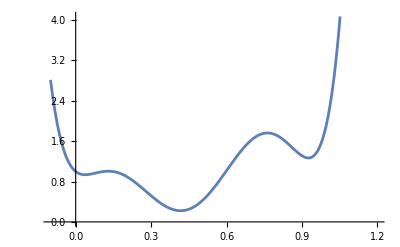

```mathematica
um=1;
Subscript[α, 1]=-um/2;Subscript[α, 2]=um/2;Subscript[α, 3]=um/2;Subscript[α, 4]=-um/2;Subscript[α, 5]=-um/2;Subscript[α, 6]=um/2;
Subscript[phi, 1][ζ_]:=-LegendreP[1,2*ζ-1];
Subscript[phi, 2][ζ_]:=LegendreP[2,2*ζ-1];
Subscript[phi, 3][ζ_]:=-LegendreP[3,2*ζ-1];
Subscript[phi, 4][ζ_]:=LegendreP[4,2*ζ-1];
Subscript[phi, 5][ζ_]:=-LegendreP[5,2*ζ-1];
Subscript[phi, 6][ζ_]:=LegendreP[6,2*ζ-1];
u[ζ_]:=um+Subscript[α, 1]*Subscript[phi, 1][ζ]+Subscript[α, 2]*Subscript[phi, 2][ζ]+Subscript[α, 3]*Subscript[phi, 3][ζ]+Subscript[α, 4]*Subscript[phi, 4][ζ]+Subscript[α, 5]*Subscript[phi, 5][ζ]+Subscript[α, 6]*Subscript[phi, 6][ζ];
Plot[u[ζ],{ζ,-0.1,1.2}]
```

```mathematica
Expand[u[ζ],ζ]
```

1-4 ζ+78 ζ^2-500 ζ^3+1225 ζ^4-1260 ζ^5+462 ζ^6

```mathematica
LegendreP[3,2*x-1]
```

-1+12 x-30 x^2+20 x^3